# CG and Arnoldi

We want to understand the connection between CG and Arnoldi for a SPD matrix A.  We continue to focus on solving
	A.x=b
starting from an initial guess of x_0.

### CG Algorithm

The CG algorithm we looked is initialized by
	 r_0 | = | b-A.x_0
 p_0 | = | r_0
the iteration is
	α_j | = | (r_j,r_j)/(A.p_j,p_j)
 x_(j+1) | = | x_j+α_j p_j
r_(j+1) | = | r_j-α_j A.p_j
β_j | = | (r_(j+1),r_(j+1))/(r_j,r_j)
p_(j+1) | = | r_(j+1)+ β_j p_j

### Lanczos Process

Specializing the Arnoldi Process to a symmetric matrix A produces numerous simplifications and efficiencies. As noted the "Hessenberg" matrix H becomes a symmetric tridiagonal matrix T satisfying
	A.Q_k=Q_(k+1).T_k 
With the diagonal of T_k given by α_1,α_2,…,α_k and the sub and super diagonals given by β_2,β_3,…,β_k with the last row containing a lonely β_(k+1).

Question: Are the α  and β  in CG and Lanczos the same?

The first column says 
	A.q_1=α_1 q_1+β_2 q_2
which gives
	β_2 q_2=A.q_1-α_1 q_1
Since (q_2,q_1)=0 this gives
	0=(A.q_1,q_1)-α_1(q_1,q_1)
Since (q_1,q_1)=(q_2,q_2)=1 we have
	α_1 | = | (A.q_1,q_1)
β_2 | = | ||A.q_1-α_1 q_1||.

For j=2:k  the columns satisfy
	A.q_j=β_j q_(j-1)+α_j q_j+β_(j+1)q_(j+1)
which gives
	β_(j+1)q_(j+1)=A.q_j-α_j q_j-β_j q_(j-1)
As before α_j is determined by the orthogonality of the q vectors
	 0=(A.q_j-α_j q_j).q_j-0
so 
	α_j=(A.q_j,q_j).
As before β_(j+1) is determined by the normalization
	β_(j+1)=||A.q_j-α_j q_j-β_j q_(j-1)||.
Here is a manual implementation

```mathematica
{m,k}={12,4};
(* Create Symmetric Test Matrix *)
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
(* Initialization *)
q1=Normalize[RandomReal[{-1,1},m]];
(* Step j=1 *)
α1=Dot[A.q1,q1];
q2=A.q1-α1 q1;
β2=Norm[q2];
q2=q2/β2;
(* Step j=2 *)
α2=Dot[A.q2,q2];
q3=A.q2-α2 q2-β2 q1;
β3=Norm[q3];
q3=q3/β3;
(* Step 3 *)
α3=Dot[A.q3,q3];
q4=A.q3-α3 q3-β3 q2;
β4=Norm[q4];
q4=q4/β4;
(* Step 4 *)
α4=Dot[A.q4,q4];
q5=A.q4-α4 q4-β4 q3;
β5=Norm[q5];
q5=q5/β5;
(* Build Q and T *)
Q={q1,q2,q3,q4,q5}ᵀ;
T=({{α1, β2, 0, 0}, {β2, α2, β3, 0}, {0, β3, α3, β4}, {0, 0, β4, α4}, {0, 0, 0, β5}});
(* Check residuals *)
Map[Norm,{A.Q⟦All,1;;-2⟧-Q.T,Qᵀ.Q-IdentityMatrix[5]}]
```

{3.70334×10^-16,1.13966×10^-15}

I am going to make a command that builds this

```mathematica
AASLanczos[A_,r_,k_]:=Module[
{q1=Normalize[r],Q,T,α,q,β},
(* Constructing Q and T *)
Q=ConstantArray[0,{Length[A],k+1}];
T=SparseArray[{},{k+1,k}];
(* Initialization *)
Q⟦All,1⟧=q1;
α=Dot[A.q1,q1];
q=A.q1-α q1;
β=Norm[q];
q=q/β;
Q⟦All,2⟧=q;
T⟦1,1⟧=α;
T⟦2,1⟧=T⟦1,2⟧=β;
(* Iteration *)
Do[
α=Dot[A.q,q];
q=A.q-α q-β Q⟦All,j-1⟧;
β=Norm[q];
q=q/β;
Q⟦All,j⟧=q;
T⟦j,j⟧=α;
T⟦j+1,j⟧=T⟦j,j+1⟧=β,
{j,2,k}];
(* Returning Stuff *)
{Q,T}
]
```

I am pre-building a test problem

```mathematica
{m,k}={12,4};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r=RandomReal[{-1,1},m];

{Q,T}=AASLanczos[A,r,k];
Map[Dimensions,{Q,T}];
Qᵀ.Q
MatrixForm[T]
```

Set::partw: Part 5 of T$11184⟦j,j+1⟧ does not exist.

{{1.,-8.46545×10^-16,1.45717×10^-15,0.370568,0.},{-8.46545×10^-16,1.,-0.449612,0.473027,0.},{1.45717×10^-15,-0.449612,1.,-0.817846,0.},{0.370568,0.473027,-0.817846,1.,0.},{0.,0.,0.,0.,0.}}

(1.0017 | 3.26251 | 0 | 0
3.26251 | 0.129995 | 1.45556 | 0
0 | 1.45556 | 3.43808 | 3.23737
0 | 0 | 3.23737 | -1.37953
0 | 0 | 0 | 3.95841)

FIX FOR MONDAY!!

Dot::dotsh: Tensors SparseArray[Automatic,{5,4},0,{1,{{0,2,3,3,3,3},{{1},{2},{1}}},{0.0785622,3.22632,3.22632}}] and {{-0.0398009,-0.112204,0,0,0},{0.395453,0.274127,0,0,0},{-0.100423,0.38106,0,0,0},«6»,{0.246301,-0.514387,0,0,0},«2»} have incompatible shapes.

Dot::dotsh: Tensors {{0.0785622,3.22632,0,0},{3.22632,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} and {{-0.0398009,-0.112204,0,0,0},{0.395453,0.274127,0,0,0},{-0.100423,0.38106,0,0,0},«6»,{0.246301,-0.514387,0,0,0},«2»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{1.,Max[√Root[1.36424×10^-12 Conjugate[{1}.1]^3 ({1}.{1})^2+(1+3+1) #1+1+1+#1^4&,1],2,√Root[1]]}
 |  |  |  |

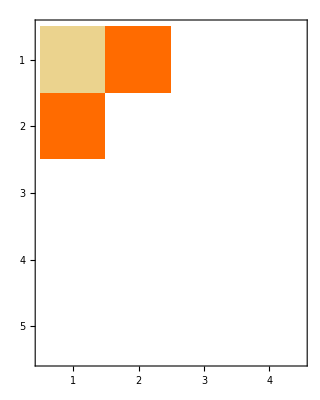

```mathematica
Map[Norm,{Qᵀ.Q-IdentityMatrix[k+1],A.Q⟦All,1;;k⟧-T.Q}]
MatrixPlot[T]
```